```mathematica
f[x_]:=Sin[x]
```

```mathematica
f'[x]
(f[x])^2+(f'[x])^2
Integrate[f[x],x]
```

Cos[x]

Cos[x]^2+Sin[x]^2

-Cos[x]

```mathematica
Simplify[%3]
```

1



```mathematica
Plot[f[x],{x,0,2 π}]
```

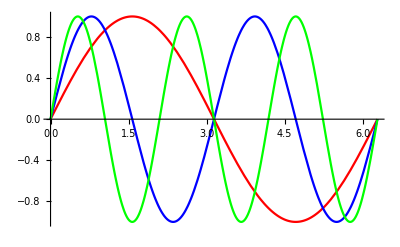

```mathematica
Plot[{f[x],f[2x],f[3x]},{x,0,2 π}, PlotStyle->{Red, Blue, Green}]
```

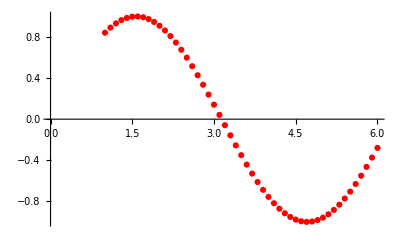

```mathematica
Table[{i,Sin[i]},{i,1,6,0.1}];
ListPlot[%,PlotStyle->Red]
```

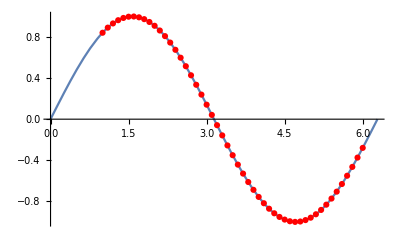

```mathematica
Show[{Plot[f[x],{x,0,2 π}],%12}]
```

{{y[x]→ⅇ^-x}}

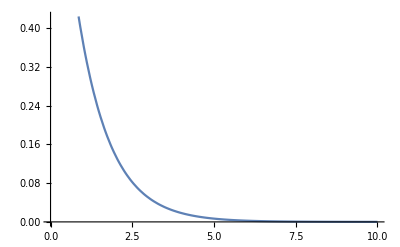

```mathematica
DSolve[{y'[x]==-y[x],y[0]==1},y[x],x]
Plot[y[x]/.%19,{x,0,10}]
```

```mathematica
NDSolve[{y'[x]==-y[x],y[0]==1},y[x],{x,0,10}]
Plot[y[x]/.%19,{x,0,10}]
```

{{y[x]→InterpolatingFunction[{{0., 10.}}, <>][x]}}

-Graphics-

```mathematica
RSolve[{y[n+1]==(1-h)y[n], y[0]==1},y[n],n]
```

{{y[n]→(1-h)^n}}